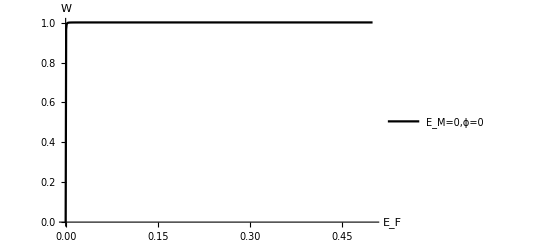

```mathematica
kbT = 1;                (*T = 115mK, E0 and Ef are in units of μeV*)
df[E0_,Ef_] := (ⅇ^((E0-Ef)/kbT)/((1+ⅇ^((E0-Ef)/kbT))^2 kbT));
(*Partial derivative of Fermi function with respect to incident electron energy*)







fact = 10000;

(*Defining the transmission probability*)

T1[E0_,Ef_,Ep_,phi_,Em_] := ⅇ^(-Im[E0/fact]-Im[Ef/fact]+Im[phi]) Abs[((1+ⅇ^((ⅈ (E0+Ef))/(2 fact))) Ep (ⅇ^((ⅈ Ef)/(2 fact)) (1+√(1-2 Ep)) Ep+2 ⅇ^((ⅈ E0)/(2 fact)) (-1-√(1-2 Ep)+(2+√(1-2 Ep)) Ep)))/((1+√(1-2 Ep)) (ⅇ^((ⅈ E0)/(2 fact)) (1+√(1-2 Ep)-2 Ep)-ⅇ^((ⅈ Ef)/(2 fact)) Ep+ⅇ^((ⅈ (E0+2 Ef))/(2 fact)) √(1-2 Ep) Ep-ⅇ^((ⅈ (2 E0+3 Ef))/(2 fact)) √(1-2 Ep) Ep+ⅇ^((ⅈ (2 E0+Ef))/(2 fact)) (1+√(1-2 Ep)) (-1+2 Ep)-ⅇ^((ⅈ (3 E0+2 Ef))/(2 fact)) (1+√(1-2 Ep)) (-1+2 Ep)+ⅇ^((ⅈ (4 E0+3 Ef))/(2 fact)) (1+√(1-2 Ep)-2 Ep) (-1+2 Ep)+ⅇ^((ⅈ (3 E0+4 Ef))/(2 fact)) (Ep-2 Ep^2)))]^2





(*Different values of Em in μeV*)
Emaj = 10;



(*Different elements of the Onsager matrix, change last input of transmission probability to change Em*)
LeTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),0,phi,0,Em])(df[E0/kbT,Ef/kbT])
LeVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(0)) (T1[(E0),0,phi,0,Em])(df[E0/kbT,Ef/kbT])
LhVv[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(1)) (T1[(E0),0,phi,0,Em])(df[E0/kbT,Ef/kbT])
LhTt[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ] :=( ((E0 - (Ef))/kbT)^(2)) (T1[(E0),0,phi,0,Em])(df[E0/kbT,Ef/kbT])

LeV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[ LeVv[(E0), fer,Em,phi], {E0, -Infinity, Infinity}, PrecisionGoal->2, AccuracyGoal->Infinity]

LeT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LeTt[(E0), fer, Em,phi]    , {E0, -Infinity, Infinity}, PrecisionGoal->2, AccuracyGoal->Infinity]

LhV[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LhVv[(E0), fer, Em,phi]        , {E0, -Infinity, Infinity}, PrecisionGoal->2, AccuracyGoal->Infinity]

LhT[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ] := NIntegrate[LhTt[(E0), fer, Em,phi]  , {E0, -Infinity, Infinity}, PrecisionGoal->2, AccuracyGoal->Infinity]


(*Thermoelectric parameters acquired from the Onsager matrix elements*)
k[fer_, Em_, phi_] :=(1/(2))((LeT[fer, Em, phi])^2/(2*(LeV[fer, Em, phi]*LhT[fer, Em, phi])-(LeT[fer, Em, phi]*LhV[fer, Em, phi])))
p[fer_, Em_, phi_] := (1/(4*1)) * ((LeT[fer, Em, phi])^2)/LeV[fer, Em, phi]
S[fer_, Em_, phi_] := -LeT[fer, Em, phi]/LeV[fer, Em, phi]
kappa[fer_, Em_, phi_] := ((LeV[fer, Em, phi]*LhT[fer, Em, phi] - LhV[fer, Em, phi]*LeT[fer, Em, phi])/ (LeV[fer, Em, phi]))/3.285
P[fer_, Em_, phi_] := (LhV[fer, Em, phi]/LeV[fer, Em, phi])(1)
z0[fer_, Em_, phi_] := Em*11.5*(LeV[fer, Em, phi](S[fer, Em, phi])^2/(kappa[fer, Em, phi]))/(1)
Nmax[fer_, Em_, phi_]:=(Sqrt[z0 [fer, Em, phi] + 1] - 1)/(Sqrt[z0[fer, Em, phi] + 1] + 1)
Pmaxr[fer_, Em_, phi_]:= Sqrt[(LhT[fer, Em, phi])(LeV[fer, Em, phi]*LhT[fer, Em, phi] - LhV[fer, Em, phi]*LeT[fer, Em, phi])/(LeV[fer, Em, phi])]
W[fer_, Em_, phi_] := kappa[fer, Em, phi]/LeV[fer, Em, phi]









Plot[{W[0,0,Ep]}, {Ep, 0,1/2}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotPoints->10, PlotRange->All]
Plot[{W[0,0,Ep]}, {Ep, 0,1/2}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotPoints->10, PlotRange->All]
Plot[{W[0,0,Ep]}, {Ep, 0,1/2}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotPoints->10, PlotRange->All]
Plot[{W[0,0,Ep]}, {Ep, 0,1/2}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotPoints->10, PlotRange->All]





(*Plot[{kappa[10,10, Ep]/LeV[10, 10, Ep]}, {Ep, 0,1/2}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]

Plot[{kappa[-10,10, Ep]/LeV[-10, 10, Ep]}, {Ep, 0,1}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]*)



(*Plotting the functions*)
(*
Plot[{S[fer, 0, 0],S[(fer),Emaj, 0],S[fer, 0, Pi/6],S[(fer),Emaj, Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["S", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10,PlotRange->All]
Plot[{P[fer, 0,0],P[(fer),Emaj,0],P[fer, 0,Pi/6],P[(fer),Emaj,Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["P", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10,PlotRange->All]
Plot[{kappa[fer, 0,0], kappa[fer,Emaj,0],kappa[fer, 0,Pi/6], kappa[fer,Emaj,Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]
Plot[{kappa[fer, 0, 0]/LeV[fer,0, 0], kappa[fer,Emaj, 0]/LeV[fer, Emaj, 0], kappa[fer, 0, Pi/6]/LeV[fer,0, Pi/6], kappa[fer,Emaj, Pi/6]/LeV[fer, Emaj, Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]
Plot[{kappa[0, Emaj, 0]/LeV[0,Emaj, 0], kappa[10,Emaj, 0]/LeV[10, Emaj, 0], kappa[0, Emaj, Pi/6]/LeV[0,Emaj, Pi/6], kappa[10,Emaj, Pi/6]/LeV[10, Emaj, Pi/6]}, {Emaj, -20,20}, AxesLabel->{Text[Style["E_F", FontSize->20]], Text[Style["W", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick},{Yellow, Dashed, Thick}, {Darker[Darker[Green]], Dashed, Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"}, PlotPoints->10, PlotRange->All]
*)

(*
Plot[{p[fer,0, 0], p[fer,Emaj,0], p[fer,0, Pi/6], p[fer,Emaj, Pi/6]}, { fer, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P_Max", FontSize->20]]},PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Green,Dashed,Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10, PlotRange->All]
Plot[{k[fer,0, 0], k[fer,Emaj,0], k[fer,0, Pi/6], k[fer,Emaj, Pi/6]},  {fer, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["η_maxP", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Green,Dashed,Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10, PlotRange->All]
Plot[{z0[fer,0, 0], z0[fer,Emaj,0], z0[fer,0, Pi/6], z0[fer,Emaj, Pi/6]},  {fer, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["Z_T", FontSize->20]]},PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Green,Dashed,Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10, PlotRange->All]
Plot[{Pmaxr[fer,0, 0], Pmaxr[fer,Emaj,0], Pmaxr[fer,0, Pi/6], Pmaxr[fer,Emaj, Pi/6]},  {fer, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P^r", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Green,Dashed,Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10, PlotRange->All]
Plot[{kappa[fer,0, 0], kappa[fer,Emaj,0], kappa[fer,0, Pi/6], kappa[fer,Emaj, Pi/6]}, {fer, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["κ", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Green,Dashed,Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10, PlotRange->All]
Plot[{Nmax[fer,0, 0], Nmax[fer,Emaj,0], Nmax[fer,0, Pi/6], Nmax[fer,Emaj, Pi/6]},  {fer, -20,20}, AxesLabel->{Text[Style["Ef(meV)", FontSize->20]], Text[Style["P^r", FontSize->20]]}, PlotStyle->{{Black, Thick},{Red, Dashed, Thick}, {Orange, Dashed, Thick}, {Green,Dashed,Thick}}, PlotLegends->{"E_M=0,ϕ=0", "E_M≠0,ϕ=0", "E_M=0,ϕ=π/6", "E_M≠0, ϕ=π/6"},PlotPoints->10, PlotRange->All]
*)
```